# Autologous Chemotaxis for Stokes Flow Past an Ellipsoid

## Clear All Variables and Import Packages

```mathematica
ClearAll["Global`*"];
ClearAll[Derivative];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"]
```

## Set the Parameters and Ranges

```mathematica
(*We set the conditions on the ellipsoidal geometry.*)
```

```mathematica
inner=1;outer=200;
sigmaVals=Table[i,{i,1.1,1.2,0.02}];
nsolns = Length[sigmaVals];
```

```mathematica
(*Set the biochemical and fluid parameters.*)
```

```mathematica
α=0.74;β=0.05;eps=0.01;γ=β/(1+α);
```

```mathematica
χ0[r_,θ_]:=γ/r;
```

```mathematica
χ1[r_,θ_]:=γ/2(-1+α/((1+α)r)+(1-3/(2 r)+(3+α)/(2+α)*3/(4 r^2)-1/(4 r^3))Cos[θ]);
```

```mathematica
χ[r_,θ_]:=χ0[r,θ]+eps χ1[r,θ];
```

## Define Various Geometric Functions

```mathematica
(*Express the usual spherical coordinates in terms of the deformed spherical coordinates and give the inverse transformations.*)
```

```mathematica
rEll[s1_,u1_,v1_,σ_]:=s1 σ^(-1/3)Sqrt[1+(σ^2-1)Cos[u1]^2];
θEll[s1_,u1_,v1_,σ_]:=ArcCos[(σ Cos[u1])/Sqrt[1+(σ^2-1)Cos[u1]^2]];
ϕEll[s1_,u1_,v1_,σ_]:=v1;
```

```mathematica
sSph[r_,θ_,ϕ_,σ_]:=r σ^(1/3)Sqrt[1+(σ^-2-1)Cos[θ]^2];
uSph[r_,θ_,ϕ_,σ_]:=ArcCos[(σ^-1 Cos[θ])/Sqrt[1+(σ^-2-1)Cos[θ]^2]];
vSph[r_,θ_,ϕ_,σ_]:=ϕ;
```

```mathematica
(*When deforming the cell, we need to preserve volume. Also, define the surface element and total surface area.*)
```

```mathematica
areaEleEll[s1_,u1_,v1_,σ_]:=σ^(1/3)s1^2 Sin[u1] √(1+(σ^-2-1)Cos[u1]^2);
```

```mathematica
(*Apparently, Mathematica processes Sqrt[x] and √x differently... Try replacing the stuff below with Sqrt[...] to see this! The result is in a different, but equivalent form.*)
```

```mathematica
totAreaEll[s1_,σ_]:=Integrate[areaEleEll[s1,u1,v1,σ],{u1,0,π},{v1,0,2π}];
αEll[α_,s1_,σ_]:=(4 π s1^2 α)/totAreaEll[s1,σ];
βEll[β_,s1_,σ_]:=(4 π s1^2 β)/totAreaEll[s1,σ];
```

```mathematica
(*The last major piece that we need is the Jacobian*)
```

```mathematica
JacSph[s1_,u1_,v1_,σ_]:={{σ^(1/3)/Sqrt[1+(σ^2-1)Cos[u1]^2],s1/σ(σ^2-1)Sin[u1] Cos[u1],0},{0,1/(2 σ)(1+σ^2+(σ^2-1)Cos[2 u1]),0},{0,0,1}};
```

## Find the Stream Function and Use It to Compute the Flow Lines... FIX ME.

```mathematica
(*Enter the equation for the distance to the surface of the ellipsoid parametrized by θ and s.*)
```

```mathematica
rSurf[s_,θ_,σ_]:=(s σ^(-1/3))/Sqrt[1+(σ^-2-1)Cos[θ]^2];
```

```mathematica
(*Let m that describes the number of terms we use in the expansion (see paper on flow around eggs). For a given n, there are two terms, so taking "m" gives 2m terms in the series.

There are two boundary conditions/equations that we need to satisfy on the surface. To find 2m unknowns, we need 2m equations, which corresponds to m points. Randomly generate the θ values by randomly sampling cos(θ). Now we need a module that can setup and solve the system of equations for the coefficients in the series. 

The matrix can be very singular, so using the singular value decomposition can help for stable numerics. The number of zero/ small elements on the diagonal in the "middle" matrix in the decomposition is a measure of how singular it is.*)
```

```mathematica
getCoeffsSV[s_,σ_,m_,SampTheta_]:=Module[{matrix,uu,ww,vv,proto,Bvector,coeffVecPre,coeffVec,samp=SampTheta,thetaCase,n},
(*First, we construct the matrix that multiplies the matrix of coefficients.*)
matrix=Table[0,{i,1,2m},{j,1,2m}];
Do[If[i≤m,thetaCase=samp[[i]];,thetaCase=samp[[i-m]];];
(*If i≤m, use the angular condition, otherwise use the radial condition.*)
(*If j≤m, set the a terms, otherwise, set the b terms.*)
If[(i≤m)&&(j≤m),
n=j+1;
matrix[[i,j]]=-rSurf[s,thetaCase,σ]^(-n+1)*LegendreP[n-1,Cos[thetaCase]];];
If[(i≤m)&&(j>m),
n=j+1-m;
matrix[[i,j]]=-rSurf[s,thetaCase,σ]^(-n+3)*LegendreP[n-1,Cos[thetaCase]];];
If[(i>m)&&(j≤m),
n=j+1;
matrix[[i,j]]=(1-n)rSurf[s,thetaCase,σ]^-n*GegenbauerC[n,-1/2,Cos[thetaCase]];];
If[(i>m)&&(j>m),
n=j+1-m;
matrix[[i,j]]=(3-n)rSurf[s,thetaCase,σ]^(-n+2)*GegenbauerC[n,-1/2,Cos[thetaCase]];];
,{i,1,2m},{j,1,2m}];
(*Obtain the singular value decomposition of the matrix... matrix=uu.ww.Transpose[vv], with uu, vv unitary.*)
{uu,ww,vv}=SingularValueDecomposition[matrix];
(*The action of the matrix on the vector of coefficients must be the opposite of the contribution from the flow at infinity. We construct this vector.*)
proto=Table[0,{i,1,2m}];
Do[thetaCase=samp[[i]];
proto[[i]]=rSurf[s,thetaCase,σ]^2 Cos[thetaCase];
,{i,1,m}];
Do[thetaCase=samp[[i-m]];
proto[[i]]=-rSurf[s,thetaCase,σ](1-Cos[thetaCase]^2);
,{i,m+1,2m}];
Bvector=Transpose[{proto}];
(*Our system may be written uu.ww.Transpose[vv].x=b. Applying Transpose[uu] gives ww.Transpose[vv].x=Transpose[uu].b. Next, we introduce y=Transpose[vv].x so that ww.y=Transpose[uu].b. We solve for y, then compute x via x=vv.y.*)
coeffVecPre=LinearSolve[ww,Transpose[uu].Bvector];
coeffVec=vv.coeffVecPre;
Return[{matrix,coeffVec}];
];
```

```mathematica
(*Define the functions that compute the general stream functions and velocity profiles. You need to be careful with order of operations/ substitution when differentiation is involved.*)
```

```mathematica
(*I checked the exact expression for the sphere, my scalar ψ is correct.*)
ψ[r_,θ_,ϕ_,m_,coeffVec_]:=r^2/2(1-Cos[θ]^2)+Sum[(coeffVec[[n,1]]*r^-n+coeffVec[[n+m,1]]*r^(-n+2))*GegenbauerC[n+1,-1/2,Cos[θ]],{n,1,m}];
```

```mathematica
(*The spherical basis vector is r\hat{θ}. After multiplying the θ-component by r, this matches the exact expression. It looks like the flow lines are correct.*)
velSph[r_,θ_,ϕ_,m_,coeffVec_]:=1/(r^2 Sin[θ]){D[ψ[r,θ1,ϕ,m,coeffVec],θ1],-D[ψ[r1,θ,ϕ,m,coeffVec],r1],0}/.{r1->r,θ1->θ};
```

```mathematica
velEllFromSph[s1_,u1_,v1_,σ_,m_,coeffVec_]:=JacSph[s1,u1,v1,σ].velSph[rEll[s1,u1,v1,σ],θEll[s1,u1,v1,σ],ϕEll[s1,u1,v1,σ],m,coeffVec];
```

## Compute the Solutions

```mathematica
(*Empirically, I found that m=50 generated ~ 10% error in the coefficients from trial to trial. Decreasing it ignores important terms, which leads to higher error, while increasing it beyond 70 makes the problem high-dimensional, which also increases error.*)
```

```mathematica
m=50;
```

```mathematica
(*Create the object to store the solutions.*)
```

```mathematica
y00Int=Table[0,{i,1,nsolns}];
y10Int=Table[0,{i,1,nsolns}];
```

```mathematica
(*Having all 100 different terms is a pain... Truncate the coefficients using Chop.*)
```

```mathematica
Do[σ=sigmaVals[[i]];
(*Since δ has been specified, find the radius, receptor density, and coefficients*)
αCase=αEll[α,inner,σ];
βCase=βEll[β,inner,σ];
coeffs=Chop[getCoeffsSV[inner,σ,m,ArcCos[RandomReal[{-1,1},m]]][[2]],10^-2.5];
(*The components of the velocity in the deformed coordinates don't depend on v1, since ψ doesn't depend on ϕ. I look for azimuthally symmetric solutions.*)
soln=NDSolveValue[{σ^(2/3)((Sin[u1]^2+σ^-2 Cos[u1]^2)D[V[s1,u1],{s1,2}]+s1^-1(1+Cos[u1]^2+σ^-2 Sin[u1]^2)D[V[s1,u1],{s1,1}]+s1^-2(σ^-2 Sin[u1]^2+Cos[u1]^2)D[V[s1,u1],{u1,2}]+s1^-2(Cot[u1]-2(1-σ^-2)Sin[u1]Cos[u1])D[V[s1,u1],{u1,1}]+2/s1(1-σ^-2)Sin[u1]Cos[u1]D[V[s1,u1],{s1,1},{u1,1}])== eps*velEllFromSph[s1,u1,0,σ,m,coeffs].{D[V[s1,u1],s1],D[V[s1,u1],u1],0}+NeumannValue[-βCase+αCase V[s1,u1],s1==inner],
DirichletCondition[V[s1,u1]==0,s1==outer]},
V,{s1,inner,outer},{u1,0,π}];
y00Int[[i]]=NIntegrate[αCase*areaEleEll[inner,u1,v1,σ]*soln[1,u1],{u1,0,π},{v1,0,2 π}];
(*The last factor is Cos[θ] in ellipsoidal coordinates.*)
y10Int[[i]]=NIntegrate[αCase*areaEleEll[inner,u1,v1,σ]*soln[1,u1]*(σ Cos[u1])/Sqrt[1+(σ^2-1)Cos[u1]^2],{u1,0,π},{v1,0,2 π}];
Clear[soln];
,{i,1,nsolns}]
```

## Analyze the Data

```mathematica
means=y10Int/y00Int;
vars=1/y00Int;
```

```mathematica
Sqrt[(vars/means^2)]
```

{4237.95,4212.93,4189.57,4165.99,4144.39,4122.98}

```mathematica
Transpose[{sigmaVals-1,Sqrt[(vars/means^2)]}]
```

{{0.1,4237.95},{0.12,4212.93},{0.14,4189.57},{0.16,4165.99},{0.18,4144.39},{0.2,4122.98}}

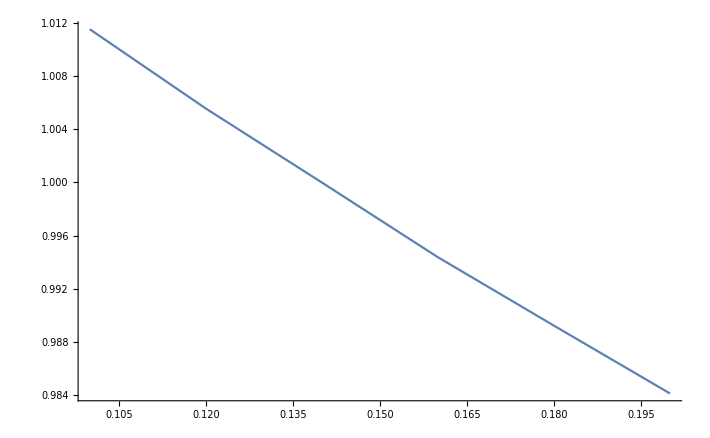

```mathematica
NSRData2=Transpose[{sigmaVals-1,Sqrt[(vars/means^2)/(vars[[Ceiling[nsolns/2]]]/means[[Ceiling[nsolns/2]]]^2)]}];
ListPlot[NSRData2,Joined->True]
```

## Testing Goes Here

```mathematica
L1={{-0.19999999999999996,4732.830332794173},{-0.17999999999999994,4688.48169583865},{-0.15999999999999992,4645.311860287909},{-0.1399999999999999,4597.909131431268},{-0.12,4564.704166111173}};
```

```mathematica
L2={{-0.09999999999999998,4534.062728446022},{-0.07999999999999996,4499.398194964128},{-0.05999999999999994,4466.696060474678},{-0.040000000000000036,4430.811257916644},{-0.020000000000000018,4402.891256168698}};
```

```mathematica
L3={{0.,4373.658987557739},{0.020000000000000018,4344.463823742038},{0.040000000000000036,4310.115632145241},{0.06000000000000005,4289.44380927179},{0.08000000000000007,4263.291526957149}};
```

```mathematica
L4={{0.10000000000000009,4237.9505573097285},{0.1200000000000001,4212.928583542137},{0.14000000000000012,4189.571518404964},{0.16000000000000014,4165.989584830737},{0.18000000000000016,4144.394204023209},{0.20000000000000018,4122.9818417272745}};
```

```mathematica
totList=Union[L1,L2,L3,L4];
totNumPts=Length[totList];
normSecondCol=totList[[All,2]]/totList[[Ceiling[totNumPts/2],2]];
totListNorm=Transpose[{totList[[All,1]],normSecondCol}];
```

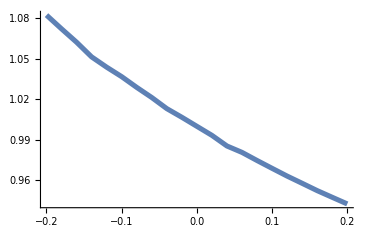

```mathematica
ListPlot[totListNorm,Joined->True,PlotStyle->{Thickness[0.01]},TicksStyle->Directive["Label", 12]]
```